```mathematica
TableForm[
Table[
Map[
{#[[1,1]],SetsToSymbol2[#[[1,2]]],With[
{g=Graph[GraphFromSets[#[[1,2]]],VertexLabels->"Name"]},
{EdgeCount[g],VertexCount[g]}
],#[[2]]}&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[k,4]}],
#1[[1]]==#2[[1]]&
]
]
],
{k,5,9}
],TableDepth->2]
```

{{2,1,1,1},v1x2x3x45,{9,5},10} |  |  |  |  | 
{{2,2,1,1},v1x2x34x56,{13,6},45} | {{3,1,1,1},v1x2x3x456,{12,6},20} |  |  |  | 
{{2,2,2,1},v1x23x45x67,{18,7},105} | {{3,2,1,1},v1x2x34x567,{17,7},210} | {{4,1,1,1},v1x2x3x4567,{15,7},35} |  |  | 
{{2,2,2,2},v12x34x56x78,{24,8},105} | {{3,2,2,1},v1x23x45x678,{23,8},840} | {{3,3,1,1},v1x2x345x678,{22,8},280} | {{4,2,1,1},v1x2x34x5678,{21,8},420} | {{5,1,1,1},v1x2x3x45678,{18,8},56} | 
{{3,2,2,2},v12x34x56x789,{30,9},1260} | {{3,3,2,1},v1x23x456x789,{29,9},2520} | {{4,2,2,1},v1x23x45x6789,{28,9},1890} | {{4,3,1,1},v1x2x345x6789,{27,9},1260} | {{5,2,1,1},v1x2x34x56789,{25,9},756} | {{6,1,1,1},v1x2x3x456789,{21,9},84}

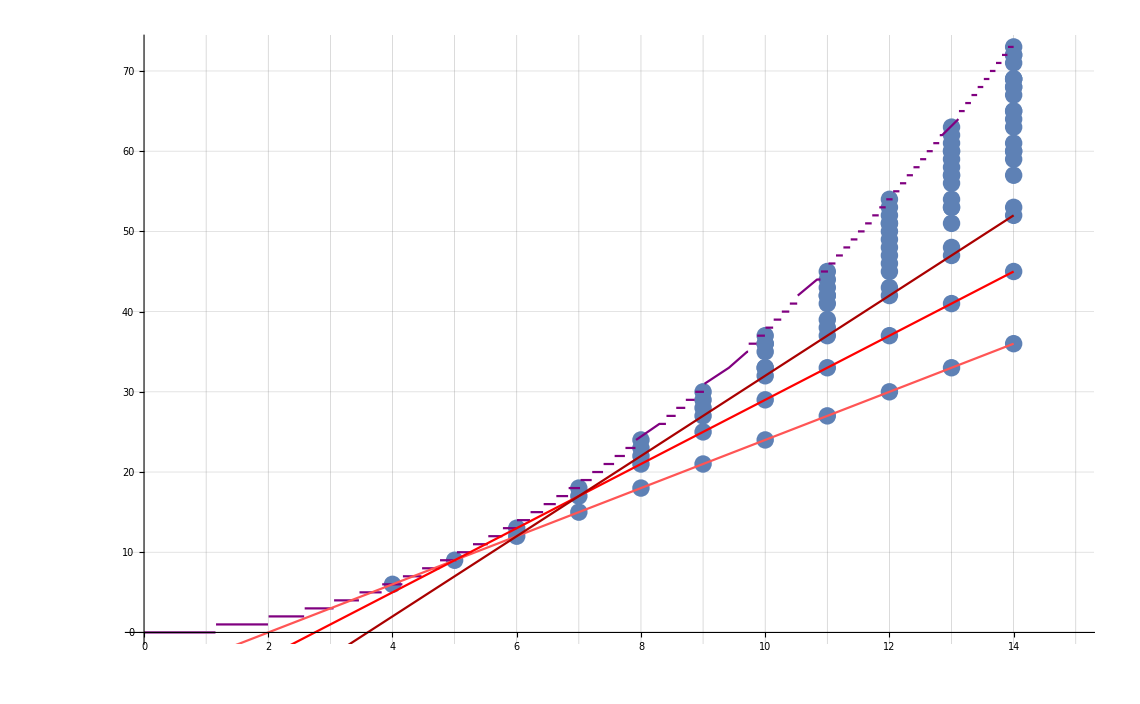

```mathematica
With[
{max=14},
Monitor[
Show[

ListPlot[
{
Flatten[

Table[
Map[
With[
{g=Graph[GraphFromSets[#[[1,2]]],VertexLabels->"Name"]},
{VertexCount[g],EdgeCount[g]}
]&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[k,4]}],
#1[[1]]==#2[[1]]&
]
]
],
{k,4,max}
],
1]
},
PlotRange->{{0,max+1},All},
GridLines->{Range[100],Automatic}],
Plot[Ceiling[(3*n^2-4)/8],{n,0,max},PlotStyle->Purple],
Plot[3*(n-2),{n,0,max},PlotStyle->Lighter[Red]],
Plot[4*(n-3)+1,{n,0,max},PlotStyle->Red],
Plot[5*(n-4)+2,{n,0,max},PlotStyle->Darker[Red]](*,
Plot[6*(n-5)+3,{n,4,max},PlotStyle->Darker[Red]],
Plot[7*(n-6)+4,{n,4,max},PlotStyle->Darker[Red]],*),
Framed-> True
],{g,k}]
]
```

```mathematica
Monitor[
Flatten[

Table[
Max[
Map[
With[
{g=Graph[GraphFromSets[#[[1,2]]],VertexLabels->"Name"]},
EdgeCount[g]
]&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[k,4]}],
#1[[1]]==#2[[1]]&
]
]
]],
{k,4,13}
],
1],{g,k}]
```

{6,9,13,18,24,30,37,45,54,63}

```mathematica
Monitor[
Flatten[

Table[
Min[
Map[
With[
{g=Graph[GraphFromSets[#[[1,2]]],VertexLabels->"Name"]},
EdgeCount[g]
]&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[k,4]}],
#1[[1]]==#2[[1]]&
]
]
]],
{k,4,13}
],
1],{g,k}]
```

{6,9,12,15,18,21,24,27,30,33}

```mathematica
LinearRecurrence[{2,-1,0,1,-2,1},{0,0,1,3,6,9},48] (*Jean-François Alcover,Sep 21 2017*)
```

{0,0,1,3,6,9,13,18,24,30,37,45,54,63,73,84,96,108,121,135,150,165,181,198,216,234,253,273,294,315,337,360,384,408,433,459,486,513,541,570,600,630,661,693,726,759,793,828}

```mathematica
Monitor[
Flatten[

Table[
Min[
Drop[
Sort[
Map[
With[
{g=Graph[GraphFromSets[#[[1,2]]],VertexLabels->"Name"]},
EdgeCount[g]
]&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[k,4]}],
#1[[1]]==#2[[1]]&
]
]
]
],1
]],
{k,4,10}
],
1],{g,k}]
```

{∞,∞,13,17,21,25,29}

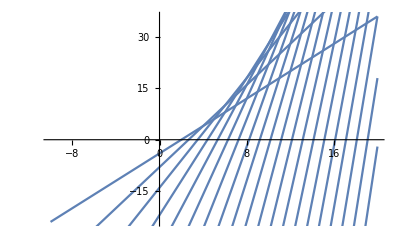

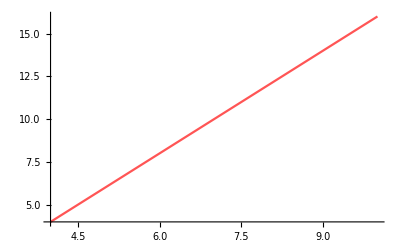
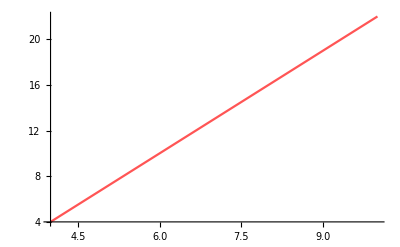
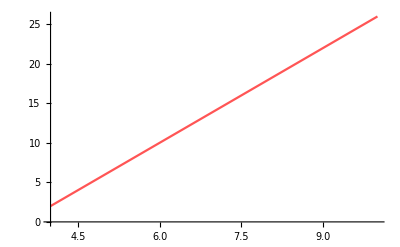
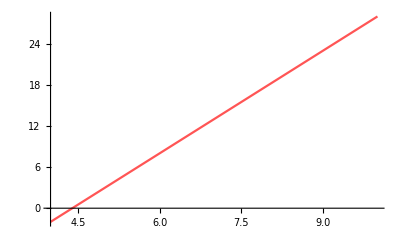
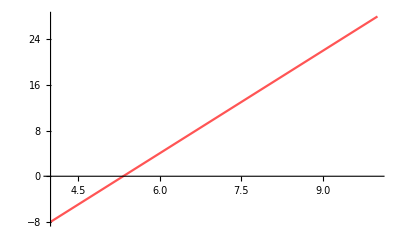
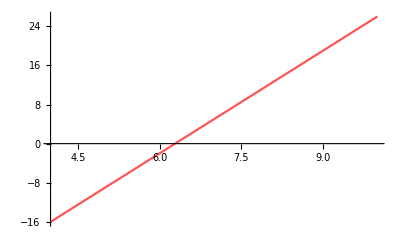
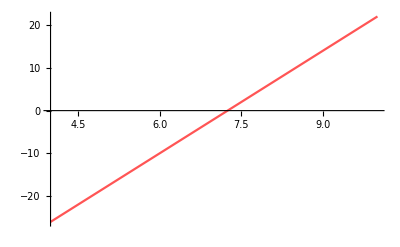

```mathematica
Show[With[{max=20},
Table[

Plot[(k+1)*(n-(k+1))+(k-1),{n,-10,1*max}],
{k,1,max}
]
]
]
```

## Now with 3 blocks

```mathematica
Monitor[
Flatten[

Table[
Max[
Map[
With[
{g=Graph[GraphFromSets[#[[1,2]]],VertexLabels->"Name"]},
EdgeCount[g]
]&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[k,3]}],
#1[[1]]==#2[[1]]&
]
]
]],
{k,4,13}
],
1],{g,k}]
```

{5,8,12,16,21,27,33,40,48,56}

```mathematica
a1=Monitor[
Flatten[
Table[
Map[
With[
{g=Graph[GraphFromSets[#[[1,2]]],VertexLabels->"Name"]},
{VertexCount[g],EdgeCount[g]}
]&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[k,3]}],
#1[[1]]==#2[[1]]&
]
]
],
{k,4,17}
]
,1],{g,k}]
```

{{4,5},{5,8},{5,7},{6,12},{6,11},{6,9},{7,16},{7,15},{7,14},{7,11},{8,21},{8,20},{8,19},{8,17},{8,13},{9,27},{9,26},{9,24},{9,24},{9,23},{9,20},{9,15},{10,33},{10,32},{10,31},{10,29},{10,28},{10,27},{10,23},{10,17},{11,40},{11,39},{11,38},{11,35},{11,36},{11,34},{11,32},{11,31},{11,26},{11,19},{12,48},{12,47},{12,45},{12,45},{12,44},{12,41},{12,41},{12,39},{12,36},{12,35},{12,29},{12,21},{13,56},{13,55},{13,54},{13,52},{13,48},{13,51},{13,50},{13,47},{13,46},{13,44},{13,40},{13,39},{13,32},{13,23},{14,65},{14,64},{14,63},{14,60},{14,61},{14,59},{14,55},{14,57},{14,56},{14,53},{14,51},{14,49},{14,44},{14,43},{14,35},{14,25},{15,75},{15,74},{15,72},{15,72},{15,71},{15,68},{15,63},{15,68},{15,66},{15,62},{15,63},{15,62},{15,59},{15,56},{15,54},{15,48},{15,47},{15,38},{15,27},{16,85},{16,84},{16,83},{16,81},{16,77},{16,80},{16,79},{16,76},{16,71},{16,75},{16,73},{16,69},{16,69},{16,68},{16,65},{16,61},{16,59},{16,52},{16,51},{16,41},{16,29},{17,96},{17,95},{17,94},{17,91},{17,92},{17,90},{17,86},{17,80},{17,88},{17,87},{17,84},{17,79},{17,82},{17,80},{17,76},{17,75},{17,74},{17,71},{17,66},{17,64},{17,56},{17,55},{17,44},{17,31}}

```mathematica
b1=Table[{VertexCount[MinimalGraph[n-1]],EdgeCount[MinimalGraph[n-1]]},{n,4,17}]
```

{{4,6},{5,9},{6,12},{7,15},{8,18},{9,21},{10,24},{11,27},{12,30},{13,33},{14,36},{15,39},{16,42},{17,45}}

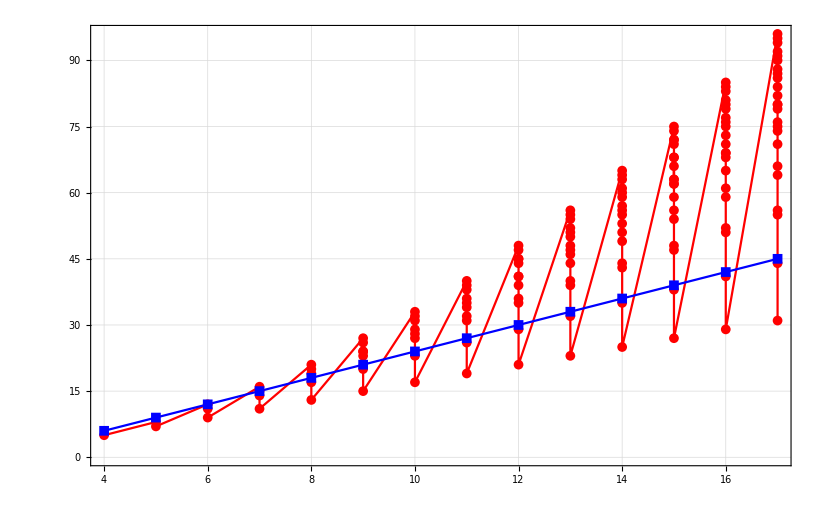

```mathematica
ListLinePlot[{a1,b1},PlotStyle->{Red,Blue},PlotMarkers->{Automatic, 10},GridLines->Automatic,Frame->True]
```

```mathematica
With[{a={5,7,9,11,13,15,17,19,21,23},b={6,9,12,15,18,21,24,27,30,33}},
Table[b[[k]]-a[[k]],{k,1,Length[a]}]
]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Table[{2n+3,3(n+1)},{n,1,10}]
```

{{5,6},{7,9},{9,12},{11,15},{13,18},{15,21},{17,24},{19,27},{21,30},{23,33}}

```mathematica
Expand[3n-6/.n->x-2]
```

-12+3 x

```mathematica
Table[{2n+3,3(n+1),3n-6},{n,1,10}]
```

{{5,6,-3},{7,9,0},{9,12,3},{11,15,6},{13,18,9},{15,21,12},{17,24,15},{19,27,18},{21,30,21},{23,33,24}}

```mathematica
FindLinearRecurrence[{5,7,9,11,13,15,17,19,21,23}]
```

{2,-1}

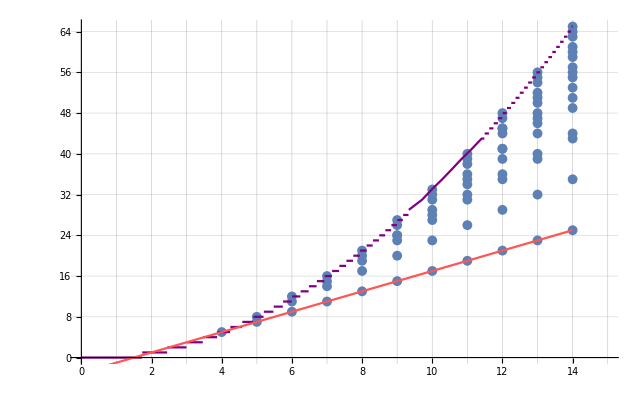

```mathematica
With[
{max=14},
Monitor[
Show[

ListPlot[
{
Flatten[

Table[
Map[
With[
{g=Graph[GraphFromSets[#[[1,2]]],VertexLabels->"Name"]},
{VertexCount[g],EdgeCount[g]}
]&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[k,3]}],
#1[[1]]==#2[[1]]&
]
]
],
{k,4,max}
],
1]
},
PlotRange->{{0,max+1},All},
GridLines->{Range[100],Automatic}],
Plot[Floor[(n^2/3)],{n,0,max},PlotStyle->Purple],
Plot[2*(n-2)+1,{n,0,max},PlotStyle->Lighter[Red]],
Framed-> True
],{g,k}]
]
```

## Now with 2 blocks

```mathematica
Monitor[
Flatten[

Table[
Max[
Map[
With[
{g=Graph[GraphFromSets[#[[1,2]]],VertexLabels->"Name"]},
EdgeCount[g]
]&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[k,2]}],
#1[[1]]==#2[[1]]&
]
]
]],
{k,4,13}
],
1],{g,k}]
```

{4,6,9,12,16,20,25,30,36,42}

```mathematica
Monitor[
Flatten[

Table[
Min[
Map[
With[
{g=Graph[GraphFromSets[#[[1,2]]],VertexLabels->"Name"]},
EdgeCount[g]
]&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[k,2]}],
#1[[1]]==#2[[1]]&
]
]
]],
{k,4,13}
],
1],{g,k}]
```

{3,4,5,6,7,8,9,10,11,12}

```mathematica
Table[EdgeCount[MinimalGraph[n-1]],{n,4,10}]
```

{6,9,12,15,18,21,24}

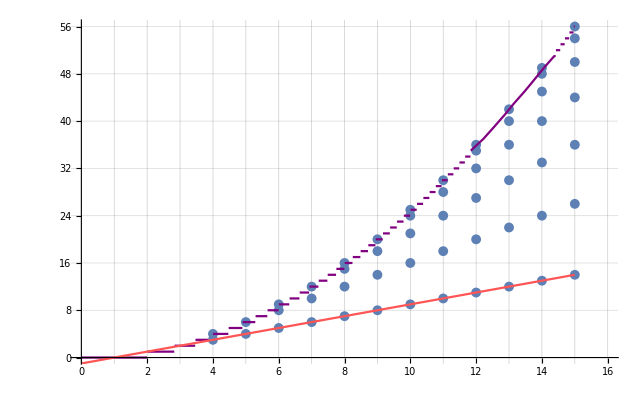

```mathematica
With[
{max=15},
Monitor[
Show[

ListPlot[
{
Flatten[

Table[
Map[
With[
{g=Graph[GraphFromSets[#[[1,2]]],VertexLabels->"Name"]},
{VertexCount[g],EdgeCount[g]}
]&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[k,2]}],
#1[[1]]==#2[[1]]&
]
]
],
{k,4,max}
],
1]
},
PlotRange->{{0,max+1},All},
GridLines->{Range[100],Automatic}],
Plot[Floor[(n^2/4)],{n,0,max},PlotStyle->Purple],
Plot[n-1,{n,0,max},PlotStyle->Lighter[Red]],
Framed-> True
],{g,k}]
]
```

## Now with 5 blocks

```mathematica
Monitor[
Flatten[

Table[
Max[
Map[
With[
{g=Graph[GraphFromSets[#[[1,2]]],VertexLabels->"Name"]},
EdgeCount[g]
]&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[k,5]}],
#1[[1]]==#2[[1]]&
]
]
]],
{k,4,11}
],
1],{g,k}]
```

{-∞,10,14,19,25,32,40,48}

```mathematica
Table[Floor[2(n+1)^2/5],{n,4,11}]
```

{10,14,19,25,32,40,48,57}

```mathematica
Monitor[
Flatten[

Table[
Min[
Map[
With[
{g=Graph[GraphFromSets[#[[1,2]]],VertexLabels->"Name"]},
EdgeCount[g]
]&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[k,5]}],
#1[[1]]==#2[[1]]&
]
]
]],
{k,4,11}
],
1],{g,k}]
```

{∞,10,14,18,22,26,30,34}

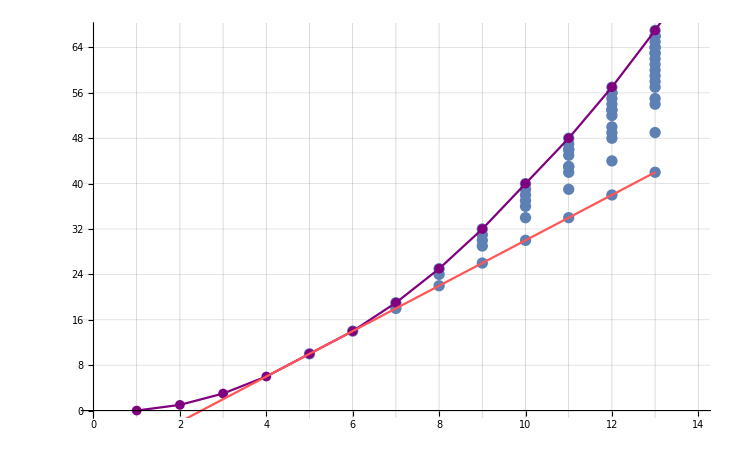

```mathematica
With[
{max=13},
Monitor[
Show[

ListPlot[
{
Flatten[

Table[
Map[
With[
{g=Graph[GraphFromSets[#[[1,2]]],VertexLabels->"Name"]},
{VertexCount[g],EdgeCount[g]}
]&,

Sort[
Tally[
Table[
{PartitionType[part],part},{part,KSetPartitions[k,5]}],
#1[[1]]==#2[[1]]&
]
]
],
{k,4,max}
],
1]
},
PlotRange->{{0,max+1},All},
GridLines->{Range[100],Automatic}],
ListLinePlot[Table[Floor[2(n+1)^2/5],{n,0,max}],PlotStyle->Purple,PlotMarkers->{Automatic, 10}],
Plot[4(n-3)+2,{n,0,max},PlotStyle->Lighter[Red]],
Framed-> True
],{g,k}]
]
```

```mathematica
D[2(n+1)^2/5,n]
```

(4 (1+n))/5

```mathematica
Table[IntegerPartitions[k,{5}]//Length,{k,5,20}]
```

{1,1,2,3,5,7,10,13,18,23,30,37,47,57,70,84}